```mathematica
W[n_]:=Exp[-ⅈ 2π/n]
```

```mathematica
Dmat[n_]:=Table[W[n]^(i j),{i,0,n-1},{j,0,n-1}]
```

```mathematica
FT[l_]:=Dmat[Length[l]].l
```

```mathematica
freqpow[l_]:=1/Length[l] Norm[l]^2/Length[l]
```

```mathematica
timpow[l_]:=Length[l]freqpow[l]
```

```mathematica
x=Table[Sin[2π*1/8 n],{n,0,63}]
```

```mathematica
FT[RotateRight[x,2]]//N
```

```mathematica
FT[x]
```

```mathematica
TensorProduct[{1,2},{a,b}]
```

```mathematica
{1,2}{a,b}
```

```mathematica
FT[x]//N
```

```mathematica
FT[RotateRight[x,2]]//N
```

```mathematica
FT[RotateRight[x,2]]//N
```

```mathematica
Chop[FT[RotateRight[x,2]]-(FT[x]Table[W[64]^(2j),{j,0,63}])//N]
```

```mathematica
ListPlot[1/64 Abs[FT[x]],Filling->Axis,Ticks->{Table[n,{n,1,63}], Automatic}]
```

```mathematica
Chop[FT[RotateRight[Reverse[x],1]]//N]
```

{0,0,0,0,0,0,0,0,0.+32. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.-32. ⅈ,0,0,0,0,0,0,0}

```mathematica
Chop[Conjugate[FT[x]]//N]
```

{0,0,0,0,0,0,0,0,0.+32. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.-32. ⅈ,0,0,0,0,0,0,0}

```mathematica
y=Table[Cos[2 π/8 t],{t,0,63}].
```

```mathematica
TrigToExp[Sin[2 π/8 t]]
```

1/2 ⅈ ⅇ^(-1/4 ⅈ π t)-1/2 ⅈ ⅇ^((ⅈ π t)/4)

```mathematica
TrigToExp[Cos[2 π/8 t]]
```

1/2 ⅇ^(-1/4 ⅈ π t)+1/2 ⅇ^((ⅈ π t)/4)

```mathematica
//FullSimplify
```

```mathematica
Chop[FT[x Table[1/2(W[64]^(-8j)+W[64]^(8j)),{j,0,63}]//FullSimplify]//N]
```

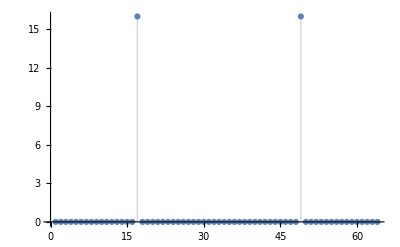

```mathematica
ListPlot[Abs[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.-16. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.+16. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}],Filling->Axis]
```

```mathematica
p1 = ListPlot[Abs[Chop[FT[x Table[1/2(W[64]^(-8j)+W[64]^(8j)),{j,0,63}]]//N]],Filling->Axis]
```

-Graphics-

```mathematica
RotateRight[FT[x]]//N//Chop
```

{0,0,0,0,0,0,0,0,0,0.-32. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.+32. ⅈ,0,0,0,0,0,0}

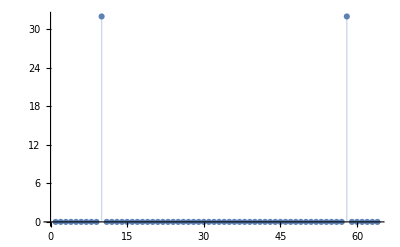

```mathematica
p2= ListPlot[Abs[RotateRight[FT[x]]//N//Chop],Filling->Axis]
```

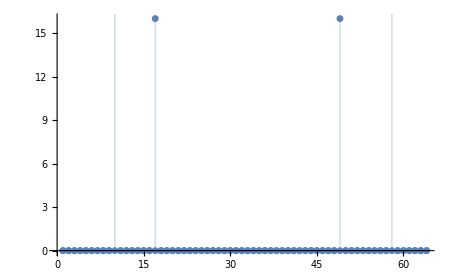

```mathematica
Show[p1,p2]
```